for n = 5,Simpson estimate is : 2.49642

2.46948

True value is 2.46948

Absolute error is 0.0269384

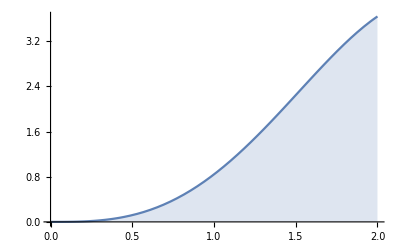

```mathematica
a = 0;
b=2;
n =5 ;
h = (b-a)/n;
y=Table[a+i*h, {i,1,n}];
f[x] := x^2Sin[x];
sumodd = 0;
sumeven = 0;
For[i=1,i<n,i+=2,sumodd +=f[x]/.x->y[[i]]];
For[i=2,i<n,i+=2,sumeven +=f[x]/.x->y[[i]]];
Sn =N[(h/2)*((f[x]/.x->a)+2* (N[sumodd]+N[sumeven]) + (f[x]/.x->b))];
Print["for n = ",n, ",Simpson estimate is : ",Sn]
in = N[Integrate[x^2Sin[x],{x,0,2}]]
Print["True value is ",in]
Print["Absolute error is ",Abs[Sn-in]]
Plot[x^2Sin[x],{x,0,2},Filling->Bottom,PlotLegends->"Expressions"]
```

for n = 4,Simpson estimate is : 0.07694

0.0767719

True value is 0.0767719

Absolute error is 0.000168106

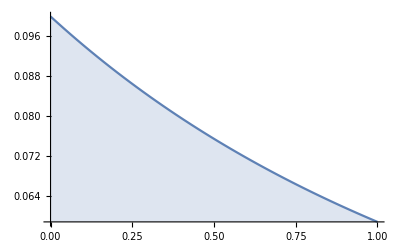

```mathematica
a = 0;
b=1;
n =4 ;
h = (b-a)/n;
y=Table[a+i*h, {i,1,n}];
f[x] := 1/(x^2+6x+10);
sumodd = 0;
sumeven = 0;
For[i=1,i<n,i+=2,sumodd +=f[x]/.x->y[[i]]];
For[i=2,i<n,i+=2,sumeven +=f[x]/.x->y[[i]]];
Sn =(h/2)*((f[x]/.x->a)+2* (N[sumodd]+N[sumeven]) + (f[x]/.x->b));
Print["for n = ",n, ",Simpson estimate is : ",Sn]
in = N[Integrate[1/(x^2+6x+10),{x,0,1}]]
Print["True value is ",in]
Print["Absolute error is ",Abs[Sn-in]]
Plot[1/(x^2+6x+10),{x,0,1},Filling->Bottom,PlotLegends->"Expressions"]
```

```mathematica
a = 0;
b=2;
n =4;
h = (b-a)/n;
y=Table[a+i*h, {i,1,n}];
f[x] := x^2Sin[x];
sumodd = 0;
sumeven = 0;
For[i=1,i<n,i+=2,sumodd +=f[x]/.x->y[[i]]];
For[i=2,i<n,i+=2,sumeven +=f[x]/.x->y[[i]]];
Sn =(h/3)*((f[x]/.x->a)+4* (N[sumodd])+2*(N[sumeven]) + (f[x]/.x->b));
Print["for n = ",n, ",Simpson estimate is : ",Sn]
in = N[Integrate[x^2Sin[x],{x,0,2}]]
Print["True value is ",in]
Print["Absolute error is ",Abs[Sn-in]]
Plot[x^2Sin[x],{x,0,2},Filling->Bottom,PlotLegends->"Expressions"]
```

for n = 4,Simpson estimate is : 2.46284

2.46948

True value is 2.46948

Absolute error is 0.00664803

-Graphics-

```mathematica
a = 0;
b=1;
n =4 ;
h = (b-a)/n;
y=Table[a+i*h, {i,1,n}];
f[x] := 1/(x^2+6x+10);
sumodd = 0;
sumeven = 0;
For[i=1,i<n,i+=2,sumodd +=f[x]/.x->y[[i]]];
For[i=2,i<n,i+=2,sumeven +=f[x]/.x->y[[i]]];
Sn =(h/3)*((f[x]/.x->a)+4* (N[sumodd])+2*(N[sumeven]) + (f[x]/.x->b));
Print["for n = ",n, ",Simpson estimate is : ",Sn]
in = N[Integrate[1/(x^2+6x+10),{x,0,1}]]
Print["True value is ",in]
Print["Absolute error is ",Abs[Sn-in]]
Plot[1/(x^2+6x+10),{x,0,1},Filling->Bottom,PlotLegends->"Expressions"]
```

for n = 4,Simpson estimate is : 0.0767728

0.0767719

True value is 0.0767719

Absolute error is 8.6186×10^-7

-Graphics-

```mathematica
x[0]=0;
y[0]=1;
a=0;
b=1;
n=10;
h=(b-a)/n;
f[x_,y_]=Exp[x]/y;
x[j_] :=x[j-1] + h;
y[j_] :=y[j-1] + h*f[x[j-1],y[j-1]];
Grid[Prepend[Table[{j,N[x[j],4],N[y[j],7]},{j,1,10}],{"j","x[j]","y[j]"}],
Dividers->{AllTrue,AllTrue}]
```

Set::write: Tag List in {1/4,1/2,3/4,1}[0] is Protected.

SetDelayed::write: Tag List in {1/4,1/2,3/4,1}[j_] is Protected.

j | x[j] | y[j]
1 | 0.1 | {0.25,0.5,0.75,1.}[1.]
2 | 0.2 | {0.25,0.5,0.75,1.}[2.]
3 | 0.3 | {0.25,0.5,0.75,1.}[3.]
4 | 0.4 | {0.25,0.5,0.75,1.}[4.]
5 | 0.5 | {0.25,0.5,0.75,1.}[5.]
6 | 0.6 | {0.25,0.5,0.75,1.}[6.]
7 | 0.7 | {0.25,0.5,0.75,1.}[7.]
8 | 0.8 | {0.25,0.5,0.75,1.}[8.]
9 | 0.9 | {0.25,0.5,0.75,1.}[9.]
10 | 1. | {0.25,0.5,0.75,1.}[10.]

```mathematica
x[0]=0;
y[0]=1;
a=0;
b=0.3;
n=3;
h=(b-a)/n;
f[x_,y_]=y+x;
x[j_] :=x[j-1] + h;
y[j_] :=y[j-1] + h*f[x[j-1]+(h/2),y[j-1]+(h/2)*f[x[j-1],y[j-1]]];
Grid[Prepend[Table[{j,N[x[j],4],N[y[j],7]},{j,1,3}],{"j","x[j]","y[j]"}],
Dividers->{AllTrue,AllTrue}]
```

Set::write: Tag List in {1/4,1/2,3/4,1}[0] is Protected.

SetDelayed::write: Tag List in {1/4,1/2,3/4,1}[j_] is Protected.

j | x[j] | y[j]
1 | 0.1 | {0.25,0.5,0.75,1.}[1.]
2 | 0.2 | {0.25,0.5,0.75,1.}[2.]
3 | 0.3 | {0.25,0.5,0.75,1.}[3.]